```mathematica
parseThm::noParse="Alas no parse. Let me know if you think this should parse!";
parseThm::noSpan="Oops no spanning parse, but here's what I've got:";
```

```mathematica
ClearAll[parseThm]
```

```mathematica
parseThm[input_]:=Module[{urlResponse}, urlResponse=URLExecute["http://puremath.wolfram.com:8080/theoremSearchTest/thmp1",{"inputString"->input,"ContentType"->"application/x-www-form-urlencoded;charset=UTF-8"}];
If[0==Length[urlResponse],Message[parseThm::noParse];Return[]];
If[Values[urlResponse[[1]]]=="NONE",Message[parseThm::noSpan]];
(*urlResponse[[1]][[4]][[2]]*)
(*{StringReplace[urlResponse[[1]][[2]][[2]]," :> ":>" -> "]}*)
ToExpression["{"<>urlResponse[[1]][[2]][[2]]<>"}"]
];
```

```mathematica
server="http://puremath.wolfram.com:8080/theoremSearchTest/thmp1";
```

```mathematica
parseThm[input_String]:=Module[{httpReq,urlResponse,server="http://puremath.wolfram.com:8080/theoremSearchTest/thmp1"}, 
httpReq=HTTPRequest[server,<|"inputString"->input,
"ContentType"->"application/json"(*"ContentType"->"application/x-www-form-urlencoded;charset=UTF-8"*)
|>];
(*urlResponse=URLExecute["http://puremath.wolfram.com:8080/theoremSearchTest/thmp1",{"inputString"->input,"ContentType"->"application/json"}];*)
urlResponse=URLRead[httpReq];
Print[httpReq];
urlResponse=ImportString[FromCharacterCode[Normal[urlResponse[[1]]]],"JSON"];
If[0==Length[urlResponse],Message[parseThm::noParse];Return[]];
Print[urlResponse[[1]]];
If[Values[urlResponse[[1]]]=="NONE",Message[parseThm::noSpan]];
(*urlResponse[[1]][[4]][[2]]*)
urlResponse[[1]][[2]][[2]]
];
```

```mathematica
HTTPRequest[server,<|"inputString"->"hi",
"ContentType"->"application/json"(*"ContentType"->"application/x-www-form-urlencoded;charset=UTF-8"*)
|>]
```

HTTPRequest[…]

```mathematica
URLExecute["http://puremath.wolfram.com:8080/theoremSearchTest/thmp1",{"inputString"->"ring","ContentType"->"application/x-www-form-urlencoded;charset=ISO-8859-1"}]
```

{{form→"WL",parsedStr→,parseStructType→NONE,stringForm→<|"WL"->NONE :>, "Scores"->{0, 1.0,  1,  1}|>},{form→long,parsedStr→[ent{name=ring}],stringForm→<|LONG->[ent{name=ring}], "Scores"->{0, 1.0}|>}}

```mathematica
parseThm["Given any function $f$, there are infinitely many roots in $g(zeta(f))$."]
```

parseThm[Given any function $f$, there are infinitely many roots in $g(zeta(f))$.]

```mathematica
Clear[myTreeForm]
```

```mathematica
myTreeForm[exp_]:=Module[{e},
(*keep the "Label", make them different color*)
(*e=exp/.{Rule[Alternatives["Type","Qualifiers","Label"],w_]:>w,List[w_]:>w};*)
e=Replace[exp,{Rule[Alternatives["Type","Qualifiers","Label"],w_]:>w,List[w_]:>w},All];
Magnify[TreeForm[e],1.001]];
```

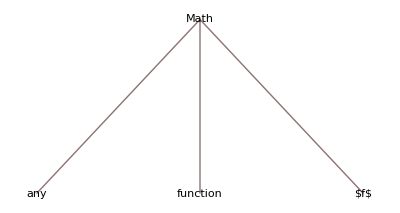

```mathematica
myTreeForm[Math["Qualifiers"->{"any"}, "Type"->"function", "Label"->"$f$"]]
```

```mathematica
mb=MakeBoxes[#, StandardForm]&@ %284
```

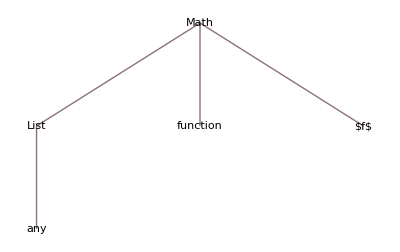

```mathematica
RawBoxes[mb/. StyleBox["Math",rest___]:> StyleBox["Math",FontColor:> RGBColor[0,1.,1.]]]
```

```mathematica
StyleBox["Math",{"StandardForm","Output",GrayLevel[0]},FontSize->Scaled[0.05],StripOnInput->False]
```

```mathematica
FullForm[%]
```

Magnify[TreeForm[Math[List["any"],"function","$f$"]],1.001]

```mathematica
(* Example *)
parseThm["Given any function $f$, there are infinitely many zeros in $g(zeta(f))$."]
```

HYP :> Math["Name"->"function", "Property"->{"any"}, "Called"->"$f$"], STM :> Reference["there"] ~HasProperty~ Math["Name"->"zero", "Property"->{"infinitely many"}, "Qualifiers" -> {"in", Math["Name"->"$g(zeta(f))$"]}]

```mathematica
parseThm1[input_]:=Module[{urlResponse}, urlResponse=URLExecute["http://puremath.wolfram.com:8080/theoremSearchTest2/thmp1",{"inputString"->input,"ContentType"->"application/json"}];
If[0==Length[urlResponse],Message[parseThm::noParse];Return[]];
If[Values[urlResponse[[1]][[6]]]=="NONE",Message[parseThm::noSpan]];
urlResponse
]
```

```mathematica
parseThm[input_]:=Module[{urlResponse}, urlResponse=URLExecute["http://puremath.wolfram.com:8080/theoremSearchTest/thmp1",{"inputString"->input,"ContentType"->"application/json"}];
ToExpression[urlResponse[[1]][[4]][[2]]]
]
```

```mathematica
parseThm2[input_]:=Module[{urlResponse}, urlResponse=URLExecute["http://puremath.wolfram.com:8080/theoremSearchTest2/thmp1",{"inputString"->input,"ContentType"->"application/json"}];
ToExpression[urlResponse[[1]][[4]][[2]]]
]
```

```mathematica
parseThm1[input_]:=Module[{urlResponse}, urlResponse=URLExecute["http://puremath.wolfram.com:8080/theoremSearchTest3/thmp1",{"inputString"->input,"ContentType"->"application/json"}];
ToExpression[urlResponse[[1]][[4]][[2]]]
]
```

```mathematica
parseThm1[" prime is called $p $"]
```

{Math[<|Name→prime|>]∈Math[<|Name→$p $|>]}

```mathematica
parseThm1["this prime is called $p $"]
```

{Math[<|Name→prime,Property→{this}|>]∈Math[<|Name→$p $|>]}

```mathematica
parseThm1["field is ring"]
```

{HasProperty[Math[<|Name→field|>],Math[<|X→"is", ,Name→ring|>]]}

```mathematica
parseThm2["given a quaternion algebra"]
```

HYP:>Math[Name→quaternion algebra]

```mathematica
parseThm2["suppose $a=b$"]
```

HYP:>Math[$a=b$]

```mathematica
parseThm1["field is ring"]
```

{{commandNumUnits→0,form→ONE TREE,numUnits→0,parsedStr→"STM" :> Math["Name"->"field"] ~HasProperty~ Math["Name"->"ring"],score→1.,stringForm→"STM" :> Math["Name"->"field"] ~HasProperty~ Math["Name"->"ring"]},{commandNumUnits→3,form→"WL",numUnits→3,parsedStr→Math["Name"->"field"] ~HasProperty~ Math["Name"->"ring"],score→1.,parseStructType→STM,stringForm→<|"WL"->STM :>Math["Name"->"field"] ~HasProperty~ Math["Name"->"ring"], "Scores"->{1.0,  3,  3}|>},{commandNumUnits→0,form→long,numUnits→0,parsedStr→assert[[ent{name=field}], verbphrase[vbs[is], [ent{name=ring}]]],score→1.,stringForm→<|LONG->assert[[ent{name=field}], verbphrase[vbs[is], [ent{name=ring}]]], "Scores"->{1.0}|>}}